```mathematica
(*Quit[]*)
```

```mathematica
ClearAll["Global`*"];
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[]
```

/run/media/bryan/Resources/Documents/Base/4. 实验/2. 穆斯堡尔效应/data

```mathematica
<<"../../MathUtils.m"
(*<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];*)
Information["Funcs`*"];
autoCollapse[];
```

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
({colors,colorsDefault}
=colorPalette/@{"Scientific","Default"})//Grid
```

RGBColor[0.9, 0.36, 0.054] | RGBColor[0.365248, 0.427802, 0.758297] | RGBColor[0.945109, 0.593901, 0.] | RGBColor[0.645957, 0.253192, 0.685109] | RGBColor[0.285821, 0.56, 0.450773] | RGBColor[0.7, 0.336, 0.] | RGBColor[0.491486, 0.345109, 0.8] | RGBColor[0.71788, 0.568653, 0.] | RGBColor[0.70743, 0.224, 0.542415] | RGBColor[0.287228, 0.490217, 0.664674] | RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636] | RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922] | RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023] | RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854] | RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

```mathematica
"### For REFERENCE ONLY ###";
"dump/20181122/data_Co.Asc";
```

```mathematica
processData[filename_]:=ToExpression[
StringSplit[
StringTrim[
Import[StringTrim[
"latest/"<>filename<>".Asc"
],"String"]
//StringSplit[#,"\n"]&
]
]
];
hideInfo[processData]
```

### processData

```mathematica
graphData[filename_,peakness_,padding_:0,opts_:{},markers_:{},peaksref_:{}]:=Module[{
data=processData[filename],
peaks=peaksref
},

"# Find data peaks in domain";
If[peaks=={},
peaks=Select[10<#⟦1⟧<500&]@(
{#⟦1⟧,-#⟦2⟧}&/@FindPeaks[-data⟦All,2⟧,Sequence@@peakness]
);
Print[peaks];
];

Show[
ListLinePlot[
data
,Sequence@@opts
,PlotTheme->"Scientific"
,Filling->Axis
,PlotRangePadding->{
{0,0},
{padding*Min[data⟦All,2⟧],0}
}
,PlotRange->{All,
MinMax[data⟦All,2⟧,Scaled[.1]]
}
,PlotRangeClipping->False
,PlotStyle->Directive[
Thickness[.001],
colors⟦2⟧
]
,ImageSize->420
,ImagePadding->{{36,42},{25,30}}
],
ListPlot[peaks
,Sequence@@markers
,PlotStyle->Directive[
colors⟦1⟧
]
]
]
];
hideInfo[graphData]
```

### graphData

```mathematica
previewData[filename_,peakness_,padding_,peaksref_:{},aspect_:1/2,markersize_:.15,ylabel_:1.06]:=Module[
{graph},

graph=graphData[filename,peakness,padding,{
AspectRatio->aspect
,Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10],#2]&)@@@{
{"道址",Scaled[{1.06,0}]},
{"计数",Scaled[{0,ylabel}]}
},{(*ADD EPILOGS HERE*)}
]
},{
PlotMarkers->{
With[{length=1.35,offset=2},
Graphics[{
Thickness[.1],
{Arrowheads[.5],Arrow[{{0,-offset-length},{0,-offset}}]}
},PlotRange->{-offset-length,0}]
],markersize}
},peaksref];

Print[Magnify[graph,2]];
Return[graph]
];
hideInfo[previewData]
```

### previewData

{{38,6588},{77,6654},{117,7136},{147,7035},{186,6819},{226,6626},{289,6629},{327,6654},{367,7062},{396,7147},{436,6633},{475,6608}}

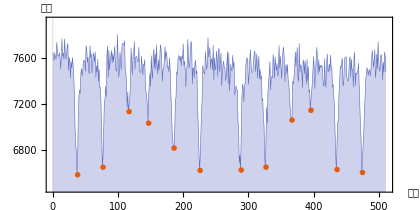

```mathematica
feRef=previewData["FeRef",{10,0,-7300},.02];
```

{{121,7852},{152,7950},{362,7795},{392,7932}}

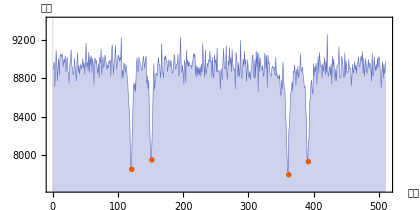

```mathematica
naRef=previewData["NaRef",{12,0,-8000},.02];
```

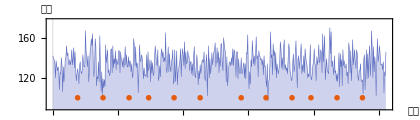

```mathematica
peaksFe={{38,6588},{77,6654},{117,7136},{147,7035},{186,6819},{226,6626},{289,6629},{327,6654},{367,7062},{396,7147},{436,6633},{475,6608}};
peaksNa={{121,7852},{152,7950},{362,7795},{392,7932}};

feTest=previewData["FeTest",{},.2,{peaksFe⟦All,1⟧,Table[100,Length[peaksFe]]}ᵀ,1/3.5,.25,1.12];
```

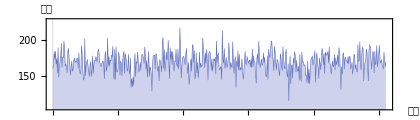
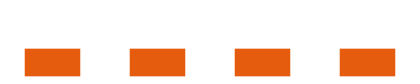

```mathematica
naTest=previewData["NaTest",{},.1,{peaksNa⟦All,1⟧,Table[125,Length[peaksNa]]}ᵀ,1/3.5,.25,1.12];
```

```mathematica
"### Some EXPERIMENTS: Recover data from img ###";
ListLinePlot[
(Plus@@(Abs[ImageData[Binarize[
Import["bg_exp.png"]
]]-1]))/27
,ImageSize->560
];
"### END OF EXPERIMENTS ###";
```

```mathematica
SetAttributes[exportGraph,HoldAll];
exportGraph[graph_]:=Export[
"plots/"<>ToString[HoldForm[graph]]<>".pdf",
ReleaseHold[graph]
];
```

```mathematica
exportGraph/@holdItems[
{feRef,naRef,feTest,naTest}
]
```

{plots/feRef.pdf,plots/naRef.pdf,plots/feTest.pdf,plots/naTest.pdf}

```mathematica
"### DATA ANALYSIS ###";
```

```mathematica
StringRiffle[#," & "]&[
ToString/@Reverse[peaksFe]⟦All,1⟧
]
```

475 & 436 & 396 & 367 & 327 & 289 & 226 & 186 & 147 & 117 & 77 & 38

```mathematica
{{pFeR,pFeL},{pNaR,pNaL}}=Function[
peaks,
{#⟦2⟧,Reverse[#⟦1⟧]}&@(
peaks⟦All,1⟧⟦#⟧&/@{1;;Length[peaks]/2,(Length[peaks]/2+1);;-1}
)
]/@{peaksFe,peaksNa};
Grid/@%
```

{289 | 327 | 367 | 396 | 436 | 475
226 | 186 | 147 | 117 | 77 | 38,362 | 392
152 | 121}

```mathematica
peaksFe⟦All,1⟧⟦{1,6,7,12}⟧
Mean[{#⟦4⟧-#⟦3⟧,#⟦2⟧-#⟦1⟧}]&@%
ScientificForm[
k=10.656/%,
5,
NumberPadding->{"", "0"}
]
```

{38,226,289,475}

187

5.6984×10^-2

```mathematica
{vcr,vcl}=Mean[{#⟦1⟧,#⟦2⟧,#⟦5⟧,#⟦6⟧}]&/@{pFeR,pFeL}//N
NumberForm[
%+{1,-1}*0.185/k,
5,
NumberPadding->{"", "0"}
]
```

{381.75,131.75}

{385.,128.5}

```mathematica
c=UnitConvert[Quantity[, "SpeedOfLight"], "Millimeters"/"Seconds"]//QuantityMagnitude;
kilo=10^3;
eByC=4.80766*10^-8;
un=QuantityMagnitude[UnitConvert[Quantity[1,"NuclearMagneton"],"eV/Tesla"]]
```

3.152451×10^-8

```mathematica
eg=Mean[
Mean[{Abs[#⟦4⟧-#⟦2⟧],Abs[#⟦5⟧-#⟦3⟧]}]&/@{pFeR,pFeL}
]*k*eByC//N
```

1.89717×10^-7

```mathematica
en=Mean[
Mean[{Abs[#⟦3⟧-#⟦2⟧],Abs[#⟦5⟧-#⟦4⟧]}]&/@{pFeR,pFeL}
]*k*eByC//N
```

1.08899×10^-7

```mathematica
#/(33*un)&/@{eg,en}
%*un
QuantityMagnitude[UnitConvert[Quantity[#,"Electronvolts"],"Joules"]]&/@%
```

{0.182366,0.104679}

{5.749×10^-9,3.29997×10^-9}

{9.21091×10^-28,5.28713×10^-28}

```mathematica
Abs[Mean[pNaR]-vcr]
Abs[Mean[pNaL]-vcl]
```

4.75

4.75

```mathematica
k*4.75
eByC*%
```

0.270674

1.30131×10^-8

```mathematica
Mean[
Abs[#⟦2⟧-#⟦1⟧]&/@{pNaR,pNaL}
]*k*eByC//N
```

8.35576×10^-8

```mathematica
Quantity[, "ReducedPlanckConstant"]
```

ℏ

```mathematica
5*eByC*k
UnitConvert[Quantity[, "ReducedPlanckConstant"]/Quantity[%/2,"Electronvolts"],"Seconds"]//QuantityMagnitude
```

1.3698×10^-8

9.61035×10^-8